```mathematica
f1[x_] := x^2/Exp[x^2]
f2[x_] :=(Sin[x])^2/2
f3[x_] := x^2/(1+x^4)
```

```mathematica
f2[x]
```

Sin[x]^2/2

```mathematica
f1[x]
```

ⅇ^(-x^2) x^2

```mathematica
f3[x]
```

x^2/(1+x^4)

```mathematica
Plot [ f1[x],f2[x],f3[x]]
```

Plot::nonopt: Options expected (instead of f3[x]) beyond position 2 in Plot[f1[x],f2[x],f3[x]]. An option must be a rule or a list of rules.

```mathematica
Plot[{f1[x],f2[x],f3[x]},{x,-2,2}, PlotLabels-> "Expressions"]
```

-Graphics-

```mathematica
h[x_]:= -0.248226 Cos[2 x] - 0.0184829 Cos[4 x] - 0.0594608 Cos[x] Sin[x] +0.123626 Sin[4 x]
```

```mathematica
h[x]
```

-0.248226 Cos[2 x]-0.0184829 Cos[4 x]-0.0594608 Cos[x] Sin[x]+0.123626 Sin[4 x]

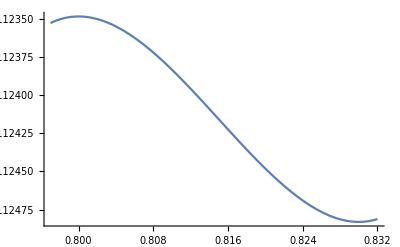

```mathematica
Plot [h[x],{x,0.797,0.832}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
villson = Table[Sin[n],{n,1001,1020}];
```

```mathematica
Max[villson]
```

Sin[1007]

```mathematica
f[x_,y_] := (x+y) Sin[x-y]
```

```mathematica
Plot3D[f[x,y],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Count[FindMaximum [f[x,y],{x,-Infinity, Infinity},{y,-Infinity, Infinity}]]
```

FindMaximum::srect: Value -∞ in search specification {x,-∞,∞} is not a number or array of numbers.

Count[FindMaximum[f[x,y],{x,-∞,∞},{y,-∞,∞}]]

```mathematica
ClearAll["Global`*"]
```

Cos[3 t]

Sin[2 t]+Sin[3 t]

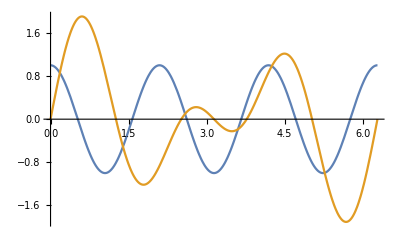

```mathematica
x= Cos[3 t]
y = Sin[2 t] + Sin[3 t]
Plot[{x,y},{t,0,2 Pi}]
```

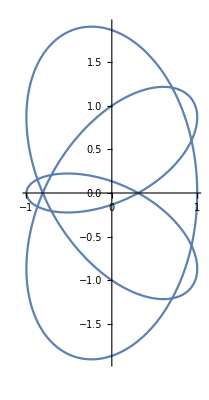

```mathematica
ParametricPlot[{Cos[3 t],Sin[2 t] + Sin[3 t]},{t,0,2 Pi}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
w[x_] := 3 Sin[x] - x
```

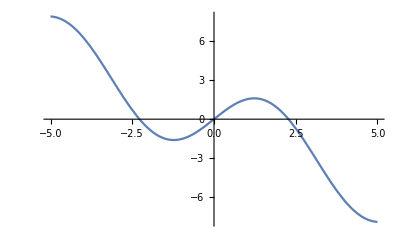

```mathematica
Plot[w[x],{x,-5,5}]
```

```mathematica
w[-2.279]
```

0.000405325

```mathematica
FindRoot[w[x]==0,{x,-2.3}]
```

{x→-2.27886}

```mathematica
FindRoot[w[x]==0,{x,2.3}]
```

{x→2.27886}

```mathematica
FindRoot[w[x]==0,{x,0}]
```

{x→0.}

```mathematica
DSolve[{y''[x]==x*Sin[y],y[0]==1, y'[0] ==1},y[x],x]
```

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[{y''[x]==x Sin[y],y[0]==1,y'[0]==1},y[x],x]

```mathematica
DSolve[{y''[x]==x Sin[y[x]],y[0]==1,y'[0]==1},y,x]
```

DSolve[{y''[x]==x Sin[y[x]],y[0]==1,y'[0]==1},y,x]

```mathematica
funktion = First[
y[x] /.NDSolve[{y''[x]==x Sin[y[x]],y[0]==1,y'[0]==1},y[x],{x,0,19}]]
```

InterpolatingFunction[…][x]

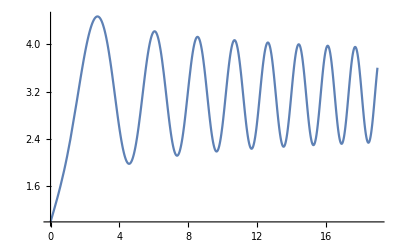

```mathematica
Plot[funktion,{x,0.,19.}]
```

```mathematica
InterpolatingFunction[{{0.,19.}},]
```

InterpolatingFunction[{{0.,19.}}]

```mathematica
h[a_]:=(4a^2-1) (x^2+y^2)-2 x y+2 a (x+y)-2 a^2
```

```mathematica
h[a]
```

-2 a^2-2 x y+2 a (x+y)+(-1+4 a^2) (x^2+y^2)==0

```mathematica
h[-1]
```

-2-2 x y-2 (x+y)+3 (x^2+y^2)==0

```mathematica
-2 (-Sqrt[1/2])^2-2 x y+2 (-Sqrt[1/2]) (x+y)+(-1+4 (-Sqrt[1/2])^2) (x^2+y^2)
```

-1+x^2-2 x y+y^2-√2 (x+y)

```mathematica
h[-1/2]
```

-1/2-x-y-2 x y==0

```mathematica
h[0]
```

-x^2-2 x y-y^2==0

```mathematica
h[1/2]
```

-1/2+x+y-2 x y==0

```mathematica
h[Sqrt[1/2]]
```

-1+x^2-2 x y+y^2+√2 (x+y)==0

```mathematica
h[-Sqrt[1/2]]
```

0

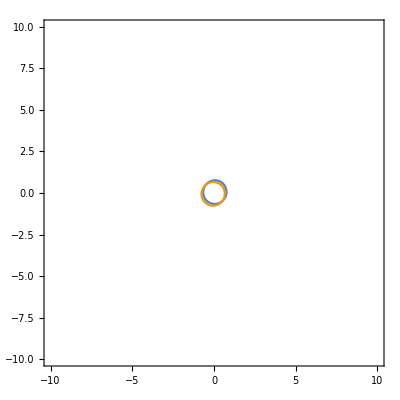

```mathematica
ContourPlot[{h[-5]==0,h[5]==0},{x,-10,10},{y,-10,10}]
```

```mathematica
1/2 // N
```

0.5

```mathematica
1/Sqrt[2] // N
```

0.707107

```mathematica
g[a_]:=(4a^2-1) (x^2+y^2)-2 x y+2 a (x+y)-2 a^2 ==0
```

```mathematica
g[-Sqrt[1/2]]
```

-1+x^2-2 x y+y^2-√2 (x+y)==0

```mathematica
h[a,x,y]
```

-2 a^2-2 x y+2 a (x+y)+(-1+4 a^2) (x^2+y^2)==0

```mathematica
-2 a^2-2 x y+2 a (x+y)+(-1+4 a^2) (x^2+y^2)==0
h[x]
```

-2 a^2-2 x y+2 a (x+y)+(-1+4 a^2) (x^2+y^2)==0

-2 x^2-2 x y+2 x (x+y)+(-1+4 x^2) (x^2+y^2)==0

```mathematica
Clear[a,x,y,u]
Manipulate[Plot[h[a], {AspectRatio -> Automatic, PlotRange -> {{-5,5}, {-5,5}}}],{a,-1,1}]
```

```mathematica
a
```

a

```mathematica
x
```

x

```mathematica
y
```

y

```mathematica
h[a]
```

-2 a^2-2 x y+2 a (x+y)+(-1+4 a^2) (x^2+y^2)==0

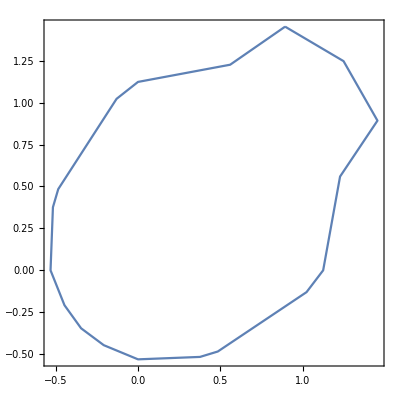

```mathematica
ContourPlot[h[-1] == 0,{x,-50,50},{y,-50,50},PlotRange -> All]
```

```mathematica
h[-1]
```

-2-2 x y-2 (x+y)+3 (x^2+y^2)==0

```mathematica
h[0]
```

-x^2-2 x y-y^2

```mathematica
Plot[h[0],{x,-10,10},{y,-10,10}]
```

Plot::nonopt: Options expected (instead of {y,-10,10}) beyond position 2 in Plot[h[0],{x,-10,10},{y,-10,10}]. An option must be a rule or a list of rules.

```mathematica
ContourPlotPlot[h[0]==0,{x,-10,10},{y,-10,10}]
```

ContourPlotPlot[-x^2-2 x y-y^2==0,{x,-10,10},{y,-10,10}]